### Gell - Mann Matrix representation of SU (3)

```mathematica
λ1={{0,1,0},{1,0,0},{0,0,0}};
λ2={{0,-ⅈ,0},{ⅈ,0,0},{0,0,0}};
λ3={{1,0,0},{0,-1,0},{0,0,0}};
λ4={{0,0,1},{0,0,0},{1,0,0}};
λ5={{0,0,-ⅈ},{0,0,0},{ⅈ,0,0}};
λ6={{0,0,0},{0,0,1},{0,1,0}};
λ7={{0,0,0},{0,0,-ⅈ},{0,ⅈ,0}};
λ8={{1,0,0},{0,1,0},{0,0,-2}}/Sqrt[3];
```

### F - spin representation of SU (3)

```mathematica
F1= λ1/2;
F2= λ2/2;
F3= λ3/2;
F4= λ4/2;
F5= λ5/2;
F6= λ6/2;
F7= λ7/2;
F8= λ8/2;
```

```mathematica
Y=2F8 / Sqrt[3];

Iplus=F1+ ⅈ F2;
Iminus=F1- ⅈ F2;
I0=F3;

Vplus=F4+ ⅈ F5;
Vminus=F4- ⅈ F5;
V0= (Vplus.Vminus-Vminus.Vplus)/2;

Uplus=F6+ ⅈ F7;
Uminus=F6- ⅈ F7;
U0= (Uplus.Uminus-Uminus.Uplus)/2;
```

#### Here we define a function which can calulate the matrix governing the system of differential equations

```mathematica
GetHamiltonian[list_]:=(s=0;Do[w= D[Part[list,iterator2,1],z]*IdentityMatrix[3];Do[w=w.Evaluate[MatrixExp[ Part[list,iterator1,1]*Part[list,iterator1,2]]],{iterator1,iterator2-1}];
w= w.Part[list,iterator2,2];Do[w=w.Evaluate[MatrixExp[-Part[list,iterator2-iterator1,1]*Part[list,iterator2-iterator1,2]]],{iterator1,iterator2-1}];s=s+w,{iterator2,Length[list]}];Return[s]);
GetPropagator[list_]:=(
w=IdentityMatrix[3];
Do[w=w.MatrixExp[ Part[list,iterator,1]*Part[list,iterator,2]],{iterator,Length[list]}];
Return[w]
);
```

```mathematica
list =List[{ⅈ ιp[z],Iplus},{ⅈ μp[z],Uplus},{ⅈ  νp[z],Vplus},
{ⅈ  ι0[z],I0},{ⅈ  y0[z],Y},{ⅈ  ey[z],IdentityMatrix[3]},
{ⅈ  νm[z],Vminus},{ⅈ  μm[z],Uminus},{ⅈ  ιm[z],Iminus}];
listOfFunctions = {ιp[z], μp[z],  νp[z],
ι0[z],y0[z],ey[z],
νm[z], μm[z], ιm[z]}
listOfDerivatives=D[#,z]&/@listOfFunctions
```

{ιp[z],μp[z],νp[z],ι0[z],y0[z],ey[z],νm[z],μm[z],ιm[z]}

{ιp'[z],μp'[z],νp'[z],ι0'[z],y0'[z],ey'[z],νm'[z],μm'[z],ιm'[z]}

```mathematica
(res=FullSimplify[GetHamiltonian[list]]);
H=({{ω0[z], g01[z], g02[z]}, {g01[z], ω1[z], g12[z]}, {g02[z], g12[z], -ω0[z]-ω1[z]}});
eqs=Thread[(Flatten[res]==Flatten[ ⅈ H])];
sol=FullSimplify[Solve[eqs,listOfDerivatives]];
eqs1=Thread[listOfDerivatives==((listOfDerivatives/.sol)[[1]])];
```

```mathematica
sol//TraditionalForm
eqs1//TraditionalForm
```

{{ιp'(z)→g01(z) ((ιp(z))^2+1)-ⅈ (g12(z) νp(z)+ιp(z) (ⅈ g02(z) νp(z)-ω0(z)+ω1(z))),μp'(z)→g01(z) (-ιp(z) μp(z)+ⅈ νp(z))+ⅈ μp(z) (g02(z) ιp(z) μp(z)-ⅈ g02(z) νp(z)+ω0(z)+2 ω1(z))+g12(z) ((μp(z))^2+1),νp'(z)→νp(z) (g01(z) ιp(z)+ⅈ (2 ω0(z)+ω1(z)))+g02(z) ((νp(z))^2+1)-ⅈ g12(z) ιp(z),ι0'(z)→-2 ⅈ g01(z) ιp(z)-g02(z) (ιp(z) μp(z)+ⅈ νp(z))+ⅈ g12(z) μp(z)+ω0(z)-ω1(z),y0'(z)→3/2 (g02(z) (ιp(z) μp(z)-ⅈ νp(z))-ⅈ g12(z) μp(z)+ω0(z)+ω1(z)),ey'(z)→0,νm'(z)→g02(z) ⅇ^(1/2 ⅈ (2 y0(z)+ι0(z)))-ⅈ ⅇ^(ⅈ ι0(z)) μm(z) (g01(z)-ⅈ g02(z) μp(z)),μm'(z)→ⅇ^(ⅈ y0(z)-1/2 ⅈ ι0(z)) (g12(z)+ⅈ g02(z) ιp(z)),ιm'(z)→ⅇ^(ⅈ ι0(z)) (g01(z)-ⅈ g02(z) μp(z))}}

{ιp'(z)==g01(z) ((ιp(z))^2+1)-ⅈ (g12(z) νp(z)+ιp(z) (ⅈ g02(z) νp(z)-ω0(z)+ω1(z))),μp'(z)==g01(z) (-ιp(z) μp(z)+ⅈ νp(z))+ⅈ μp(z) (g02(z) ιp(z) μp(z)-ⅈ g02(z) νp(z)+ω0(z)+2 ω1(z))+g12(z) ((μp(z))^2+1),νp'(z)==νp(z) (g01(z) ιp(z)+ⅈ (2 ω0(z)+ω1(z)))+g02(z) ((νp(z))^2+1)-ⅈ g12(z) ιp(z),ι0'(z)==-2 ⅈ g01(z) ιp(z)-g02(z) (ιp(z) μp(z)+ⅈ νp(z))+ⅈ g12(z) μp(z)+ω0(z)-ω1(z),y0'(z)==3/2 (g02(z) (ιp(z) μp(z)-ⅈ νp(z))-ⅈ g12(z) μp(z)+ω0(z)+ω1(z)),ey'(z)==0,νm'(z)==g02(z) ⅇ^(1/2 ⅈ (2 y0(z)+ι0(z)))-ⅈ ⅇ^(ⅈ ι0(z)) μm(z) (g01(z)-ⅈ g02(z) μp(z)),μm'(z)==ⅇ^(ⅈ y0(z)-1/2 ⅈ ι0(z)) (g12(z)+ⅈ g02(z) ιp(z)),ιm'(z)==ⅇ^(ⅈ ι0(z)) (g01(z)-ⅈ g02(z) μp(z))}

```mathematica
Table[{FullSimplify[eqs1[[j]]]},{j,1,8}] //TraditionalForm
```

(g01(z) ((ιp(z))^2+1)-ⅈ g12(z) νp(z)+ιp(z) (g02(z) νp(z)+ⅈ (ω0(z)-ω1(z)))==ιp'(z)
g12(z) ((μp(z))^2+1)+g01(z) (ⅈ νp(z)-ιp(z) μp(z))+ⅈ μp(z) (g02(z) ιp(z) μp(z)-ⅈ g02(z) νp(z)+ω0(z)+2 ω1(z))==μp'(z)
ⅈ g12(z) ιp(z)+νp'(z)==g02(z) ((νp(z))^2+1)+νp(z) (g01(z) ιp(z)+ⅈ (2 ω0(z)+ω1(z)))
2 ⅈ g01(z) ιp(z)+g02(z) μp(z) ιp(z)-ⅈ g12(z) μp(z)+ⅈ g02(z) νp(z)+ω1(z)+ι0'(z)==ω0(z)
3 ⅈ g12(z) μp(z)+2 y0'(z)==3 (g02(z) (ιp(z) μp(z)-ⅈ νp(z))+ω0(z)+ω1(z))
ey'(z)==0
ⅇ^(ⅈ ι0(z)) μm(z) (ⅈ g01(z)+g02(z) μp(z))+νm'(z)==ⅇ^(1/2 ⅈ (2 y0(z)+ι0(z))) g02(z)
μm'(z)==ⅇ^(ⅈ y0(z)-1/2 ⅈ ι0(z)) (g12(z)+ⅈ g02(z) ιp(z)))

```mathematica
ode = Join[eqs1,{ιp[0]==0,ι0[0]==0,ιm[0]==0,νp[0]==0,y0[0]==0,νm[0]==0,μp[0]==0,μm[0]==0, ey[0]==0}];
```

```mathematica
sol_numerical = NDSolve[ode/.{ω1[z]->0, ω2[z]->0, g01[z]->1+0.5z,g02[z]->1+0.5z,g12[z]->1+0.5z},listOfFunctions,{z,0,15}]
```

{{ιp[z]→InterpolatingFunction[{{0., 15.}}, <>][z],μp[z]→InterpolatingFunction[{{0., 15.}}, <>][z],νp[z]→InterpolatingFunction[{{0., 15.}}, <>][z],ι0[z]→InterpolatingFunction[{{0., 15.}}, <>][z],y0[z]→InterpolatingFunction[{{0., 15.}}, <>][z],ey[z]→InterpolatingFunction[{{0., 15.}}, <>][z],νm[z]→InterpolatingFunction[{{0., 15.}}, <>][z],μm[z]→InterpolatingFunction[{{0., 15.}}, <>][z],ιm[z]→InterpolatingFunction[{{0., 15.}}, <>][z]}}

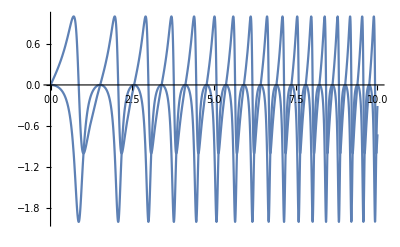

```mathematica
Plot[{Re[ιp[z]],Im[ιm[z]]}/.sol, {z,0,10}]
```

```mathematica
sol2={ι[z]->2/(ⅈ+3 Cot[3/4 z (2 1+0.5 z)])}
```

{ι[z]→2/(ⅈ+3 Cot[3/4 (2+0.5 z) z])}

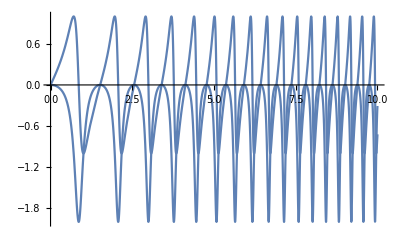

```mathematica
Plot[{Re[ι[z]],Im[ι[z]]}/.sol2, {z,0,10}]
```

```mathematica
Table[{FullSimplify[eqs1[[j]]/.{ωy}]},{j,1,8}] //TraditionalForm
```

(g01(z) ((ιp(z))^2+1)-ⅈ g12(z) νp(z)+ιp(z) (g02(z) νp(z)+ⅈ (ω1(z)-ω2(z)))==ιp'(z)
g12(z) ((μp(z))^2+1)+ⅈ μp(z) ω2(z)==(g01(z)-ⅈ g02(z) μp(z)) (ιp(z) μp(z)-ⅈ νp(z))+μp'(z)
ⅈ g12(z) ιp(z)+νp'(z)==g02(z) ((νp(z))^2+1)+νp(z) (g01(z) ιp(z)+ⅈ ω1(z))
2 ⅈ g01(z) ιp(z)+g02(z) μp(z) ιp(z)-ⅈ g12(z) μp(z)+ⅈ g02(z) νp(z)+ω2(z)+ι0'(z)==ω1(z)
3 ⅈ (g12(z) μp(z)+g02(z) νp(z))+2 y0'(z)==3 g02(z) ιp(z) μp(z)+ω1(z)+ω2(z)
ω1(z)+ω2(z)==3 ey'(z)
ⅇ^(ⅈ ι0(z)) μm(z) (ⅈ g01(z)+g02(z) μp(z))+νm'(z)==ⅇ^(1/2 ⅈ (2 y0(z)+ι0(z))) g02(z)
μm'(z)==ⅇ^(ⅈ y0(z)-1/2 ⅈ ι0(z)) (g12(z)+ⅈ g02(z) ιp(z)))

```mathematica
ws=Solve[{ωy[z]==3/2(ω0[z]+ω1[z]),ωi[z]==ω0[z]-ω1[z]},{ω0[z], ω1[z]}]
```

{{ω0[z]→1/6 (3 ωi[z]+2 ωy[z]),ω1[z]→1/6 (-3 ωi[z]+2 ωy[z])}}

```mathematica
FullSimplify[sol/.ws]
```

{{{ιp'[z]→g01[z] (1+ιp[z]^2)-ⅈ g12[z] νp[z]+ιp[z] (g02[z] νp[z]+ⅈ ωi[z]),μp'[z]→g12[z] (1+μp[z]^2)+g01[z] (-ιp[z] μp[z]+ⅈ νp[z])+1/2 μp[z] (2 g02[z] (ⅈ ιp[z] μp[z]+νp[z])-ⅈ (ωi[z]-2 ωy[z])),νp'[z]→ιp[z] (-ⅈ g12[z]+g01[z] νp[z])+g02[z] (1+νp[z]^2)+1/2 ⅈ νp[z] (ωi[z]+2 ωy[z]),ι0'[z]→-2 ⅈ g01[z] ιp[z]+ⅈ g12[z] μp[z]-g02[z] (ιp[z] μp[z]+ⅈ νp[z])+ωi[z],y0'[z]→-3/2 ⅈ (g12[z] μp[z]+g02[z] (ⅈ ιp[z] μp[z]+νp[z]))+ωy[z],ey'[z]→0,νm'[z]→ⅇ^(1/2 ⅈ (2 y0[z]+ι0[z])) g02[z]-ⅈ ⅇ^(ⅈ ι0[z]) μm[z] (g01[z]-ⅈ g02[z] μp[z]),μm'[z]→ⅇ^(ⅈ y0[z]-1/2 ⅈ ι0[z]) (g12[z]+ⅈ g02[z] ιp[z]),ιm'[z]→ⅇ^(ⅈ ι0[z]) (g01[z]-ⅈ g02[z] μp[z])}}}

2 g12[z] (1+μp[z]^2)+g01[z] (-2 ιp[z] μp[z]+2 ⅈ νp[z])+μp[z] (2 g02[z] (ⅈ ιp[z] μp[z]+νp[z])-ⅈ (ωi[z]-2 ωy[z]))==2 μp'[z]

```mathematica
solA=FullSimplify[DSolve[{D[y[x],x] *ⅈ Log[Exp[ⅈ x]]==-y[x],y[0]==1},y[x],x]]
solN=NDSolve[{D[y[x],x] *ⅈ Log[Exp[ⅈ x]]==-y[x],y[0]==1},y[x],{x,0,10}]
```

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

{}

Power::infy: Infinite expression 1/0.  + 0.\ ⅈ encountered.

NDSolve::ndnum: Encountered non-numerical value for a derivative at x == 0..

NDSolve[{ⅈ Log[ⅇ^(ⅈ x)] y'[x]==-y[x],y[0]==1},y[x],{x,1,10}]

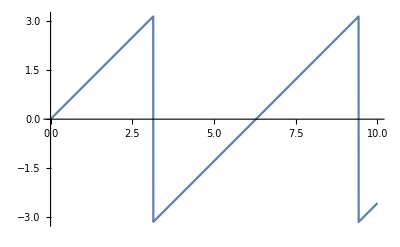

```mathematica
Plot[Im[y[x]/.solA/.{C[1]->1}],{x,0,10}]
```

```mathematica
Exp[]
```